## Decomposition QTM dI/dV in real space

### Group operators on the set {r}

```mathematica
(*Choose point in realspace away from origin*)
r0=1/(√101){1,10};
(* and rescale} *)
```

```mathematica
points1=Table[RotationMatrix[(n π)/3].(r0),{n,0,5}];
points2=Table[PauliMatrix[3].points1[[i]],{i,Length[points1]}];
points=Join[points1,points2];
```

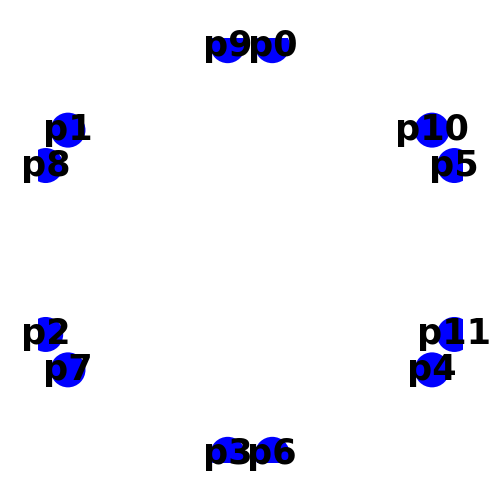

```mathematica
Show[ListPlot[points,Frame->False,Axes->False,FrameStyle->Directive[Thick,Black],FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(x\)]\)/|\!\(\*SubscriptBox[\(r\), \(0\)]\)|","\!\(\*SubscriptBox[\(r\), \(y\)]\)/|\!\(\*SubscriptBox[\(r\), \(0\)]\)|"},LabelStyle->26,ImageSize->500,PlotStyle->Blue,PlotMarkers->{Automatic,36},AspectRatio->1,Epilog->Table[Text[Style["p"<>ToString[n],35,Black,Bold],points[[n+1]],{0,-1.4}],{n,0,11}],PlotRangePadding->Scaled[.1]], Background->None]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","plot.png"}],%,Background->None]
```

C:\Users\shawn\Desktop\plot.png

```mathematica
BZ3σv1=SparseArray[{{1,10}->1,{2,11}->1,{3,12}->1,{4,7}->1,{5,8}->1,{6,9}->1,{7,4}->1,{8,5}->1,{9,6}->1,{10,1}->1,{11,2}->1,{12,3}->1,{i_,j_}/;i!=j:>0},{12,12}];
BZ3C6=SparseArray[{{1,2}->1,{2,3}->1,{3,4}->1,{4,5}->1,{5,6}->1,{6,1}->1,{7,12}->1,{8,7}->1,{9,8}->1,{10,9}->1,{11,10}->1,{12,11}->1,{i_,j_}/;i!=j:>0},{12,12}];

BZ3C3=BZ3C6.BZ3C6;
BZ3C2=BZ3C6.BZ3C3;


BZ3σv3=BZ3C3.BZ3σv1.Transpose[BZ3C3];
BZ3σv2=Transpose[BZ3C3].BZ3σv1.BZ3C3;

BZ3σd1=BZ3C2.BZ3σv1;
BZ3σd3=BZ3C3.BZ3σd1.Transpose[BZ3C3];
BZ3σd2=Transpose[BZ3C3].BZ3σd1.BZ3C3;

BZ3T1=IdentityMatrix[12];
BZ3T2=IdentityMatrix[12];
BZ3T3=IdentityMatrix[12];
```

### Analysis

#### Irrep Decomp

```mathematica
(* Representation of data points*)
χ={
Tr[IdentityMatrix[12]],
Tr[BZ3T1],
Tr[BZ3C2],
Tr[BZ3T1.BZ3C2],
Tr[BZ3C3],
Tr[BZ3C6],
Tr[BZ3σv1],
Tr[BZ3T2.BZ3σv1],
Tr[BZ3σd1],
Tr[BZ3T2.BZ3σd1]};
(* Irreps of point group *)
χA1={1,1,1,1,1,1,1,1,1,1};
χA2={1,1,1,1,1,1,-1,-1,-1,-1};
χB1={1,1,-1,-1,1,-1,1,1,-1,-1};
χB2={1,1,-1,-1,1,-1,-1,-1,1,1};
χE1={2,2,-2,-2,-1,1,0,0,0,0};
χE2={2,2,2,2,-1,-1,0,0,0,0};

χF1={3,-1,3,-1,0,0,1,-1,1,-1};
χF2={3,-1,3,-1,0,0,-1,1,-1,1};
χF3={3,-1,-3,1,0,0,1,-1,-1,1};
χF4={3,-1,-3,1,0,0,-1,1,1,-1};

(* Number of elememts in each conjugacy class*)
Cnum={1,3,1,3,8,8,6,6,6,6};
```

```mathematica
nA1=1/Tr[Cnum] Sum[χ[[i]]χA1[[i]] Cnum[[i]],{i,10}]
nA2=1/Tr[Cnum] Sum[χ[[i]]χA2[[i]] Cnum[[i]],{i,10}]
nB1=1/Tr[Cnum] Sum[χ[[i]]χB1[[i]] Cnum[[i]],{i,10}]
nB2=1/Tr[Cnum] Sum[χ[[i]]χB2[[i]] Cnum[[i]],{i,10}]

nE1=1/Tr[Cnum] Sum[χ[[i]]χE1[[i]] Cnum[[i]],{i,10}]
nE2=1/Tr[Cnum] Sum[χ[[i]]χE2[[i]] Cnum[[i]],{i,10}]


nF1=1/Tr[Cnum] Sum[χ[[i]]χF1[[i]] Cnum[[i]],{i,10}]
nF2=1/Tr[Cnum] Sum[χ[[i]]χF2[[i]] Cnum[[i]],{i,10}]
nF3=1/Tr[Cnum] Sum[χ[[i]]χF3[[i]] Cnum[[i]],{i,10}]
nF4=1/Tr[Cnum] Sum[χ[[i]]χF4[[i]] Cnum[[i]],{i,10}]
```

1

1

1

«1 more identical outputs»

2

2

0

0

0

«1 more identical outputs»

```mathematica
(* Check dimensions *)
```

```mathematica
(nA1+nA2+nB1+nB2+2nE1+2nE2+3nF1+3nF2+3nF3+3nF4)/Tr[IdentityMatrix[12]]
```

1

#### Vectors

```mathematica
id=IdentityMatrix[12];
C1ppp=id;
C2ppp=BZ3T1+BZ3T2+BZ3T3;
C3ppp=BZ3C2;
C4ppp=(BZ3T1+BZ3T2+BZ3T3).BZ3C2;
C5ppp=(id+BZ3T1+BZ3T2+BZ3T3).BZ3C3+(id+BZ3T1+BZ3T2+BZ3T3).(BZ3C3.BZ3C3);
(*C5ppp=C3+(C3.C3);*)
C6ppp=(id+BZ3T1+BZ3T2+BZ3T3).BZ3C6+(id+BZ3T1+BZ3T2+BZ3T3).(BZ3C6.BZ3C6.BZ3C6.BZ3C6.BZ3C6);
(*C6ppp=C6+(C6.C6.C6.C6.C6);*)
C7ppp=BZ3σv1+BZ3σv2+BZ3σv3+BZ3T1.BZ3σv1+BZ3T2.BZ3σv2+BZ3T3.BZ3σv3;
(*C7ppp=σv1+σv2+σv3;*)
C8ppp=(BZ3T2+BZ3T3).BZ3σv1+(BZ3T1+BZ3T3).BZ3σv2+(BZ3T1+BZ3T2).BZ3σv3;
C9ppp=BZ3σd1+BZ3σd2+BZ3σd3+BZ3T1.BZ3σd1+BZ3T2.BZ3σd2+BZ3T3.BZ3σd3;
(*C9ppp=σd1+σd2+σd3;*)
C10ppp=(BZ3T2+BZ3T3).BZ3σd1+(BZ3T1+BZ3T3).BZ3σd2+(BZ3T1+BZ3T2).BZ3σd3;

conjClasses={C1ppp,C2ppp,C3ppp,C4ppp,C5ppp,C6ppp,C7ppp,C8ppp,C9ppp,C10ppp};

Clear[A1,A2,B1,B2,E1,E2,F1,F2,F3,F4]
Subscript[P, A1]=χA1.conjClasses 1/Tr[Cnum];
Subscript[P, A2]=χA2.conjClasses 1/Tr[Cnum];
Subscript[P, B1]=χB1.conjClasses 1/Tr[Cnum];
Subscript[P, B2]=χB2.conjClasses 1/Tr[Cnum];
Subscript[P, E1]=χE1.conjClasses 1/Tr[Cnum];
Subscript[P, E2]=χE2.conjClasses 1/Tr[Cnum];
Subscript[P, F1]=χF1.conjClasses 1/Tr[Cnum];
Subscript[P, F2]=χF2.conjClasses 1/Tr[Cnum];
Subscript[P, F3]=χF3.conjClasses 1/Tr[Cnum];
Subscript[P, F4]=χF4.conjClasses 1/Tr[Cnum];


Subscript[P, A1]//Eigenvalues
Subscript[P, A2]//Eigenvalues
Subscript[P, B1]//Eigenvalues
Subscript[P, B2]//Eigenvalues
Subscript[P, E1]//Eigenvalues
Subscript[P, E2]//Eigenvalues
```

{1,0,0,0,0,0,0,0,0,0,0,0}

{1,0,0,0,0,0,0,0,0,0,0,0}

{1,0,0,0,0,0,0,0,0,0,0,0}

«1 more identical outputs»

{1/2,1/2,1/2,1/2,0,0,0,0,0,0,0,0}

{1/2,1/2,1/2,1/2,0,0,0,0,0,0,0,0}

```mathematica
Clear[A2]
Vec=Join[Table[dΙdV[Subscript[r, i]],{i,12}]];

(*Vec=Join[Table[Subscript[RA, i]+I Subscript[IA, i],{i,6}],Table[Subscript[RA, i]-I Subscript[IA, i],{i,6}]];*)
```

```mathematica
A1rep=(Subscript[P, A1]//Eigenvectors)[[1]].Vec//FullSimplify
A2rep=-(Subscript[P, A2]//Eigenvectors)[[1]].Vec//FullSimplify
B1rep=(Subscript[P, B1]//Eigenvectors)[[1]].Vec//FullSimplify
B2rep=-(Subscript[P, B2]//Eigenvectors)[[1]].Vec//FullSimplify
E1rep=Table[(Subscript[P, E1]//Eigenvectors)[[i]].Vec//FullSimplify,{i,4}]
E2rep=Table[-(Subscript[P, E2]//Eigenvectors)[[i]].Vec//FullSimplify,{i,4}]
(*(Subscript[P, E2]//Eigenvectors)[[1]].Vec//FullSimplify
(Subscript[P, E2]//Eigenvectors)[[2]].Vec//FullSimplify
(Subscript[P, E2]//Eigenvectors)[[3]].Vec//FullSimplify
(Subscript[P, E2]//Eigenvectors)[[4]].Vec//FullSimplify*)
```

dΙdV[r_1]+dΙdV[r_2]+dΙdV[r_3]+dΙdV[r_4]+dΙdV[r_5]+dΙdV[r_6]+dΙdV[r_7]+dΙdV[r_8]+dΙdV[r_9]+dΙdV[r_10]+dΙdV[r_11]+dΙdV[r_12]

dΙdV[r_1]+dΙdV[r_2]+dΙdV[r_3]+dΙdV[r_4]+dΙdV[r_5]+dΙdV[r_6]-dΙdV[r_7]-dΙdV[r_8]-dΙdV[r_9]-dΙdV[r_10]-dΙdV[r_11]-dΙdV[r_12]

dΙdV[r_1]-dΙdV[r_2]+dΙdV[r_3]-dΙdV[r_4]+dΙdV[r_5]-dΙdV[r_6]-dΙdV[r_7]+dΙdV[r_8]-dΙdV[r_9]+dΙdV[r_10]-dΙdV[r_11]+dΙdV[r_12]

dΙdV[r_1]-dΙdV[r_2]+dΙdV[r_3]-dΙdV[r_4]+dΙdV[r_5]-dΙdV[r_6]+dΙdV[r_7]-dΙdV[r_8]+dΙdV[r_9]-dΙdV[r_10]+dΙdV[r_11]-dΙdV[r_12]

{dΙdV[r_7]-dΙdV[r_9]-dΙdV[r_10]+dΙdV[r_12],-dΙdV[r_7]-dΙdV[r_8]+dΙdV[r_10]+dΙdV[r_11],dΙdV[r_1]-dΙdV[r_3]-dΙdV[r_4]+dΙdV[r_6],-dΙdV[r_1]-dΙdV[r_2]+dΙdV[r_4]+dΙdV[r_5]}

{dΙdV[r_7]-dΙdV[r_9]+dΙdV[r_10]-dΙdV[r_12],dΙdV[r_7]-dΙdV[r_8]+dΙdV[r_10]-dΙdV[r_11],dΙdV[r_1]-dΙdV[r_3]+dΙdV[r_4]-dΙdV[r_6],dΙdV[r_1]-dΙdV[r_2]+dΙdV[r_4]-dΙdV[r_5]}

```mathematica
TeXForm[E2rep]
```

\left\{\text{dIdV}\left(r_7\right)-\text{dIdV}\left(r_9\right)+\text{dIdV}\left(r_{10}\right)-\text{dIdV}\left(r_{12}\right),\text{dIdV}\left(r_7\right)-\text{dIdV}\left(r_8\right)+\text{dIdV}\left(r_{10}\right)-\text{dIdV}\left(r_{11}\right),\text{dIdV}\left(r_1\right)-\text
   {dIdV}\left(r_3\right)+\text{dIdV}\left(r_4\right)-\text{dIdV}\left(r_6\right),\text{dIdV}\left(r_1\right)-\text{dIdV}\left(r_2\right)+\text{dIdV}\left(r_4\right)-\text{dIdV}\left(r_5\right)\right\}